```mathematica
ClearAll["Global`*"]
```

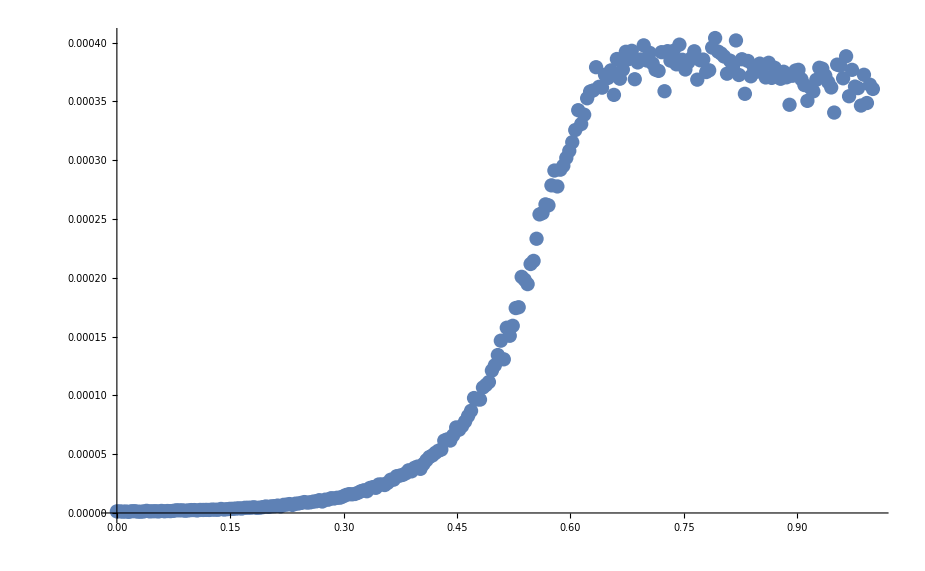

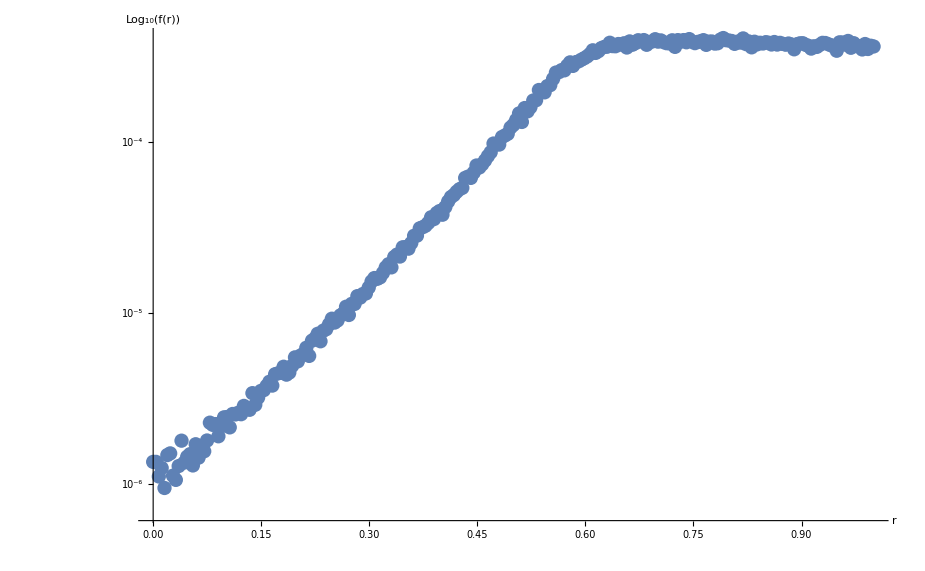

```mathematica
(* Import binary data as a 100x100 entry float3 array *)
SetDirectory[NotebookDirectory[]]; 
tableSize = 255;
rawArray= BinaryReadList["BlueNoiseRadialProfile255.complex", {"Real64","Real64"}];

radialProfileTable = Table[{i/(tableSize-1),rawArray[[Max[1,i]]][[1]]},{i,0,tableSize-1}];
logRadialProfileTable = Table[{i/(tableSize-1),Log10[rawArray[[Max[1,i]]][[1]]]},{i,0,tableSize-1}];

ListPlot[radialProfileTable]
ListPlot[logRadialProfileTable,AxesLabel->{"r","Log_10(f(r))"}];
ListLogPlot[radialProfileTable,AxesLabel->{"r","Log_10(f(r))"}]
```

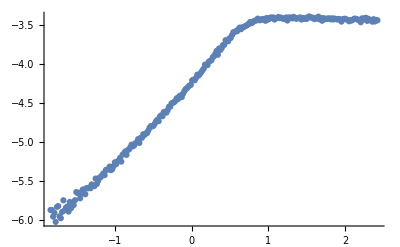

```mathematica
start=110;
end=170;
offset=start/tableSize;
scale=1/(end/tableSize - offset);
scaledLogRadialProfile=Table[{ scale*(i/(tableSize-1)-offset),Log10[rawArray[[Max[1,i]]][[1]]]}, {i,0,tableSize-1}];
ListPlot[scaledLogRadialProfile]
```

# Fitting Left Straight Line

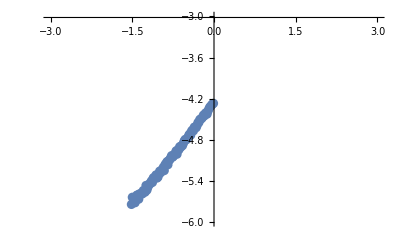

```mathematica
logProfileLeft = Table[logRadialProfileTable[[i]],{i,20,start}];
logProfileLeft = Table[scaledLogRadialProfile[[i]],{i,20,start}];
ListPlot[logProfileLeft,PlotRange->{{-3,3},{-6,-3}}]
```

{a→-4.28309,b→0.980825}

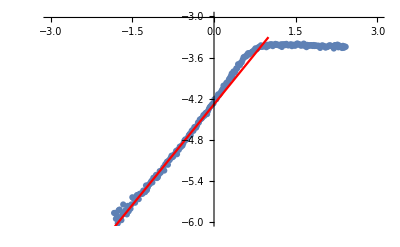

```mathematica
fittingMethod="Automatic";
model= a+b*x;
modelFitLeft=FindFit[logProfileLeft,model,{{a,-6},{b,2}},{x},Method->fittingMethod]

modelLeft=Function[{x},Evaluate[model/.modelFitLeft]];

Show[ 
ListPlot[scaledLogRadialProfile,PlotRange->{{-3,3},{-6,-3}}],
 Plot[modelLeft[x],{x,-3,1},PlotStyle->Red]
]
```

# Fitting Right Straight Line

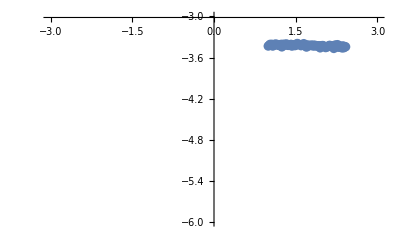

```mathematica
logProfileRight = Table[scaledLogRadialProfile[[i]],{i,end,tableSize}];
ListPlot[logProfileRight,PlotRange->{{-3,3},{-6,-3}}]
```

{a→-3.3885,b→-0.021183}

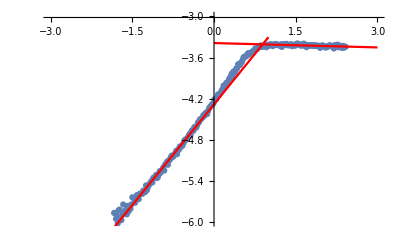

```mathematica
model= a+b*x;
modelFitRight=FindFit[logProfileRight,model,{{a,-3},{b,0}},{x},Method->fittingMethod]

modelRight=Function[{x},Evaluate[model/.modelFitRight]];

Show[ 
ListPlot[scaledLogRadialProfile,PlotRange->{{-3,3},{-6,-3}}],
 Plot[modelLeft[x],{x,-3,1},PlotStyle->Red],
Plot[modelRight[x],{x,0,3},PlotStyle->Red]
]
```

# Fitting The Middle Bend

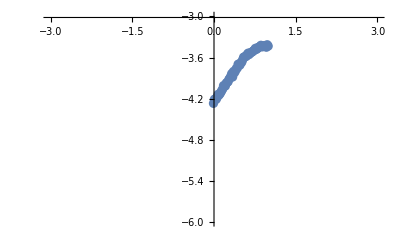

```mathematica
logProfileMiddle = Table[scaledLogRadialProfile[[i]],{i,start,end}];
ListPlot[logProfileMiddle,PlotRange->{{-3,3},{-6,-3}}]
```

{a→-4.24432,b→1.1332,c→0.398938,d→-0.72761}

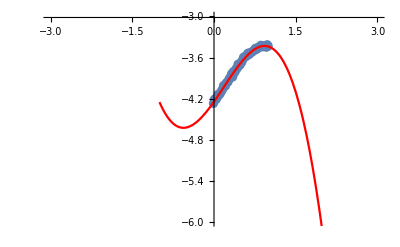

```mathematica
model= a+b*x+c*x^2;
model= a+b*x+c*x^2+d*x^3;
modelFit=FindFit[logProfileMiddle,model,{{a,-4},{b,1},{c,-1},{d,0}},{x},Method->fittingMethod]

modelMiddle=Function[{x},Evaluate[model/.modelFit]];

Show[ 
ListPlot[logProfileMiddle,PlotRange->{{-3,3},{-6,-3}}],
 Plot[modelMiddle[x],{x,-1,2},PlotStyle->Red]
]
```

## Enforcing Slope Constraints

```mathematica
positionLeft=modelLeft[0]
positionRight=modelRight[1]
slopeLeft=modelLeft'[0]
slopeRight=modelRight'[1]
```

-4.28309

-3.40969

0.980825

-0.021183

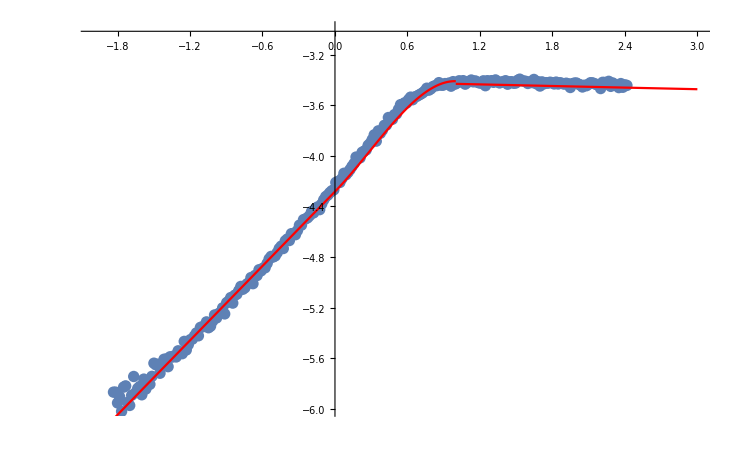

```mathematica
Clear[modelLeft,modelMiddle,modelRight]
a = positionLeft;
b=slopeLeft;
k=positionRight-a-b;
m=slopeRight-b;
c=3k-m;
d=m-2k;

modelMiddle[x_]:= a+b*x+c*x^2+d*x^3
modelLeft[x_]:=a+b*x
modelRight[x_]:=(a+b+c+d)+(b+2c+3d)*x

Show[ 
ListPlot[scaledLogRadialProfile,PlotRange->{{-2,3},{-6,-3}}],
Plot[modelMiddle[x],{x,0,1},PlotStyle->Red],
Plot[modelLeft[x],{x,-2,0},PlotStyle->Red],
Plot[modelRight[x],{x,1,3},PlotStyle->Red]
]
```

Function[{x},Piecewise[{{modelLeft[rescale[x]], rescale[x]≤0}, {modelRight[rescale[x]], rescale[x]≥1}, {modelMiddle[rescale[x]], 0≤rescale[x]≤1}}]]

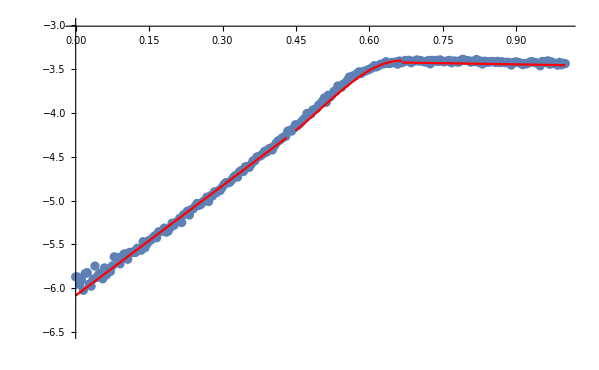

```mathematica
rescale[x_]:=offset+x/scale;
rescale[x_]:=(x-offset)*scale;
modelFull=Function[{x},Piecewise[{{modelLeft[rescale[x]],rescale[x]<=0},{ modelRight[rescale[x]],rescale[x]>=1},{ modelMiddle[rescale[x]],0<=rescale[x]<=1}}]]
(*D[modelFull]*)
Show[
ListPlot[logRadialProfileTable,PlotRange->{{0,1},{-6.5,-3}}],
Plot[modelFull[x],{x,0,1},PlotStyle->Red]
]
```

```mathematica
modelFull[0.99609375]
```

-3.43934

```mathematica
N[offset,10]
N[scale,10]
N[a,10]
N[b,10]
N[c,10]
N[d,10]
```

0.431372549

4.25

-4.28309

0.980825

0.67974

-0.787163